```mathematica
FileNameForTupleBis[primes_] := Module[{fileName, temp, sep, pPos},
    sep = "\\";
    temp = "d:\\triangle\\DataSrc";
    For[pPos = 1, pPos <= Length[primes], pPos++,
      temp = StringJoin[temp, sep, ToString[primes[[pPos]]]];
      ];
    If [Not[DirectoryQ[temp]],
   CreateDirectory[temp]
   ];
    temp = StringJoin[temp, "\\SolutionsBis.txt"];
    fileName = temp;
    Return[fileName]
   ]
```

```mathematica
CalcGoodForTuple2[tuple_, start_,end_] := Module[{sorted,fileName, file, current, index, dummy, range=1000, continue, distance,l=Length[tuple],zero=0,primeIndex=1, attempt=1},
(* always make sure the tuple is sorted *)
sorted = Sort[tuple];
fileName = FileNameForTupleBis[sorted];
index = 0;
current = 0;

(* read any existing good values - actually read the last one and store it in the current variable.   Also increment the index variable *)
If [FileExistsQ[fileName],
Monitor[
continue = True;
file = OpenRead[fileName];
While[continue,
dummy = ReadList[file, Number, range];
index += Length[dummy];
If [Length[dummy] ≠ 0, current = Last[dummy]];
If [current ≥end, continue=False];
If[Length[dummy] ≠ range, continue = False];
];
Close[file];
current +=1;
,
"Reading existing " <> fileName <> " value " <> ToString[index]
]
];
current=Max[start,current];
(* now calculate good values and append them to the file for as long as the bound is not reached *)
(* If the process is aborted, the file is closed *)
file = OpenAppend[fileName, PageWidth->40000];
CheckAbort[
Monitor[
While[current<end,
distance = Distance[current, sorted[[primeIndex]]];
current += distance;
If [distance == 0,
zero+=1;
(*Print[{current,primeIndex,zero,distance}];*)
If[zero==l,
index +=1;
zero=0;
Write[file,current];
current+=1,
attempt=0
],
zero=0
];
attempt+=1;
primeIndex=Mod[primeIndex,l]+1;
]
,
"Calculating good values " <> fileName <> ". " <> ToString[index] <> " found."<> "- " <> ToString[N[Log[10,current],50]] <> "  " <> ToString[attempt]
];
Close[file];
,
Print["Aborted at value : " <> ToString[current] ];
Close[file];
Abort[];
];
]
```

```mathematica
Timing[ CalcGoodForTuple2[{7,11,13,19},6776311148348575337205136641126709178810347048608552067007406639038209891365117880006790620472447377841127454750501983826444425539428819199196626720976487937123128028740960847919792410460478162315234450618758230565070076846446074748147739963777415049078689577711327803632236401562876317331319995315837928904303907156942558873393901897904188902376385846973627393337946096989382026505855829676472052961985009491636095134982926637916570580869555242662560553120003885061024831590819432894849498323767396642849844887725163553492719637591235884418503652335066299304027173577310702205892247828427989347689544221950138461478192310852946397184047002624730381642163036473905955015043915689489626722516917508512438860949330817072906543048228403028311142266997739808843051770921393702439259853552910415688250675600843637415022873734063684759551985910144692806909291070816071004290025894372583720754237033456695932022503917438621065453299734005275630341029714417701848808317250645222038778509869321750002182170575172221511754871851375517576017876687396088736831625320618732486146586216049446936477812543121188997909525553303667172330140049825841117809671757940511638491874052628401667302861392291077761047564173003416054032124712182643704594266198299178371039915702481593671134270863522239278765663372799591833142985368883737734121376971702302884227766253779761072760976401554679766743084243495047511398360360301809452262431495979836692174299138527300362424771110199010635792872541342702910969905736913494723846362500520856337178786596096177288988310331402578295871711290132269163947938301507663227190449599367916959948772875375466539358891052791369694098365838081320472229370926441557935167552751898843309819100582303756733596758866271084262413533659677812826018405297784491788422734625111848432898076286968030794071696163535231057763881554305962879972398125039027007071176573607554481822922358515636741398122775587908335267914258305013856535162334188405286789342416452899462733808370158250764183687891636867913646260583000120654038936558631634100840297696088652087294926381496397772370577331568355343993578815911126664163234683581936553099183168733603508105607922208681434762949909532302560261485756660907558120510060198641997057578530015695567240109210452525935810783523143333773058916950677737369054707895036169686977076762816236892338503243840058151235582458649166170806798203907503070276092595037594353752253286188306416626108967096733190931130487309045060275715308256327399008364143537405091350176959585178902359806796063442661183279414338528251961684655000313946696140733044529966700101050591205479110715177873660255599506396608760255241699675697544772571951349175657792669717136511099407055154508499924332276231003042391003531390237141911354582311962136862467236766720774126531634446643750476127810022112646486913690715339711487385393825978892547478097621968665792727348348783629960765265103612842405812887251718815179514653075650759818781223575360008527505848,10^20000]]
```

Aborted at value : 1125794828536294479427623285297270086691621260200071634555935751459062012946979209007136535702486578853206600048859882005676837779469852236149959071490350499138288746108335825497126665124125075486401617104111151162011378646227998389623296693552929845888176347871232519192540988933690019279307292619604792087619215204731554910417730406203520752329559997604451559094349829664946120570110517469049847305281450650399867558220095382605203672703495821648053228962868911158743763446023221337933416362447999015531938070761824830846118466580709626061172775815797919821043082660518268525589554316020335935942877224303903033544503320406846690377290642425390634302524440593263515840219635766061031184782744127218455773743858726686170695219714598899451283937042439989628115301152698894265754468719793651144689527556409945422743380848241055441006904250809593814567259737745365268079887805018283275023065367101856299882704548902674500480395159082888949133310458119600464393657845990231940237927710854995461219696566899108101938474048091951288102837743684660380894249930609524159874761038872196474940418681631455379849394390937283421390028561886081280297308048728435162867652740306235356739696836252671755542329463523158648506713900473324629354236218553288332952726547187621296758062163675325071276662084210697569049481309537940066959194630601102955856012379824795145294852220567243236063493862592386130471692347519589224109538904449669321572383617372676291068848053555669716555720206196152628843642841149047993606881256772743126539480343440446651224653071974421964337899614509036310494949966057851454079374322703745266302905480808633761637180077925911709345417132372377730736168343793663328972295917662762700471097298607275965803597457450126435223285195451173931669934938810906424973342700205424300322524367157837143576762307260149637554678246514521456590245349627994556348898187702404695766132947692448581337180142702900725947993832116811155686870840863939150491931315923147175655059277966625225575902376237060597137588521441142725519911903246796628899073235883885438186423541697108242399945755248270596216455612941429913243659864276878045450137863812968195757457065708400515132013730213141435674598409423865948497990347754438328858043907029427003940871065894339293083417415023230059244467902861470007639345246992251218733158975321215129373941989641085599455512684041692801585590362699391072046432421668799386183890424737975485267640297637102900678583590926690072743104933416239979399975245399198352313392297771297035605958309868860253099093617894120353337411488111882660537604151435391972410769202554647241676127011397515883761695154697562089173835443411286130854769304027295732429885798363093867713995068901376370655943157066259392655925917768081727704394781338947125562024387842635038381707288498094181817653102697165933387234909440982917846703804591350235309920591950506184758693541881678042223614860362574956369502500785199528881226860910619059889151673406937077446925320104046650035064332219128242133985072360054850504780162563683796954493211541056995067

$Aborted

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\19\SolutionsBis.txt.13372 found.-3045.0514592493487800087143083332972779619076536456 2033251
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\19\SolutionsBis.txt.13298 found.-3045.0514592493487800087143083332972779619076536456 3727630
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\19\SolutionsBis.txt.12846 found.-2957.9122714705374892640951299811134510003155044020 14884
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\19\SolutionsBis.txt.12768 found.-2957.9122714705374892640951299811134510003155044020 20311
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\19\SolutionsBis.txt.10982 found.-2957.9122714705374892640951299811134510003155044020 10133
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\19\SolutionsBis.txt.10203 found.-2957.9122714705374892640951299811134510003155044020 178159
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\19\SolutionsBis.txt.9995 found.-2957.9122714705374892640951299811134510003155044020 4940329
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\19\SolutionsBis.txt.9995 found.-2955.8309933393103135818729031422193463472530034894 519734
```

```mathematica
Calculating good values d:\triangleCalculating good values d:\triangle\DataSrc\7\11\13\19\SolutionsBis.txt.7828 found.-2955.8309933393103135818729031422193463472530034894 30751\DataSrc\7\11\13\19\SolutionsBis.txt.7546 found.-2955.8309933393103135818729031422193463472530034894 1605669
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\19\SolutionsBis.txt.8052 found.-2955.8309933393103135818729031422193463472530034894 1102
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\19\SolutionsBis.txt.7546 found.-2849.9812099765136711247056083956560296489172812433 14511518
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\19\SolutionsBis.txt.7546 found.-2915.9038926757202744184475091439807704550435446915 1016651
```

```mathematica
N[Log[10,Last[GoodForTuple[{7,11,13,19}]]]]
```

2200.16

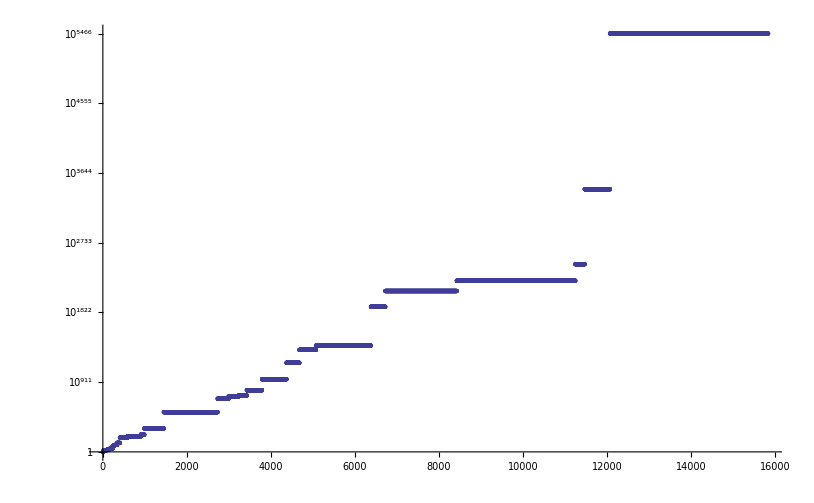

```mathematica
ListLogPlot[ReadList [FileNameForTupleBis[{3,31,43,173,229}]]]
```

```mathematica
Vals=ReadList [FileNameForTuple[{3,5,7}],Number,15000]
```

{0,1,10,10,756,757,3160,3186,3187,«14983»,18094697747096235766302058692996337413223074767552396686367448886407926788266289123060727760600413262,18094697747096235766302058692996337413223074767552396686367448886407926788266289123060727760600413275,18094697747096235766302058692996337413223074767552396686367448886407926788266289123060727760600413400,18094697747096235766302058692996337413223074767552396686367448886407926788266289123060727760600413401,18094697747096235766302058692996337413223074767552396686367448886407926788266289123060727760600413407,18094697747096235766302058692996337413223074767552396686367448886407926788266289123060727760600413410,18094697747096235766302058692996337413223074767552396686367448886407926788266289123060727760606266305,18094697747096235766302058692996337413223074767552396686367448886407926788266289123060727760606266376}

```mathematica
DigitRatio[list_,digit_]:= Length[Select[list,#==digit&]]/Length[list]
```

```mathematica
Table[Length[Select[IntegerDigits[v,7],#==d&]],{d,0,3}]
```

{52,66,71,51}

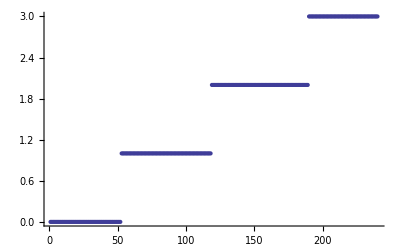

```mathematica
ListPlot[Sort[IntegerDigits[v,7]]]
```

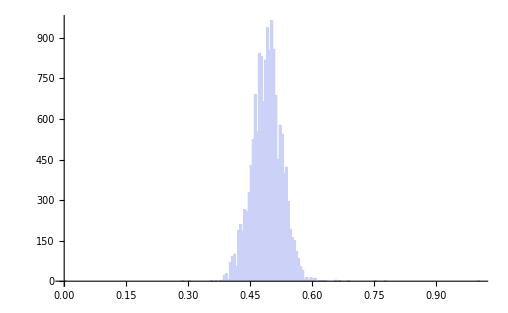
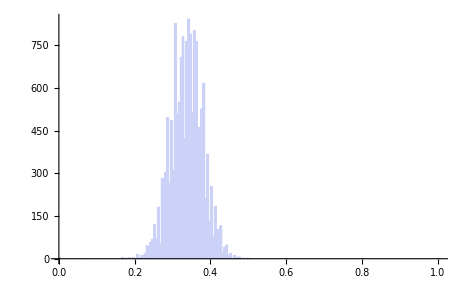
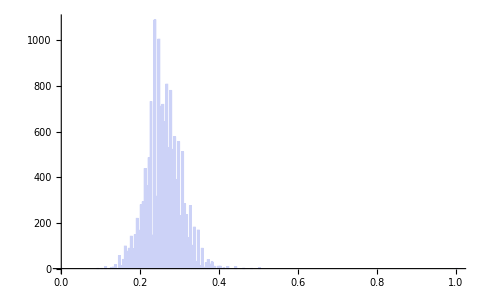

```mathematica
With[
{tuple={3,5,7}},
Table[
Histogram[
Table[
DigitRatio[IntegerDigits[v,p],1],{v,Vals}
]
],
{p,tuple}
]
]
```

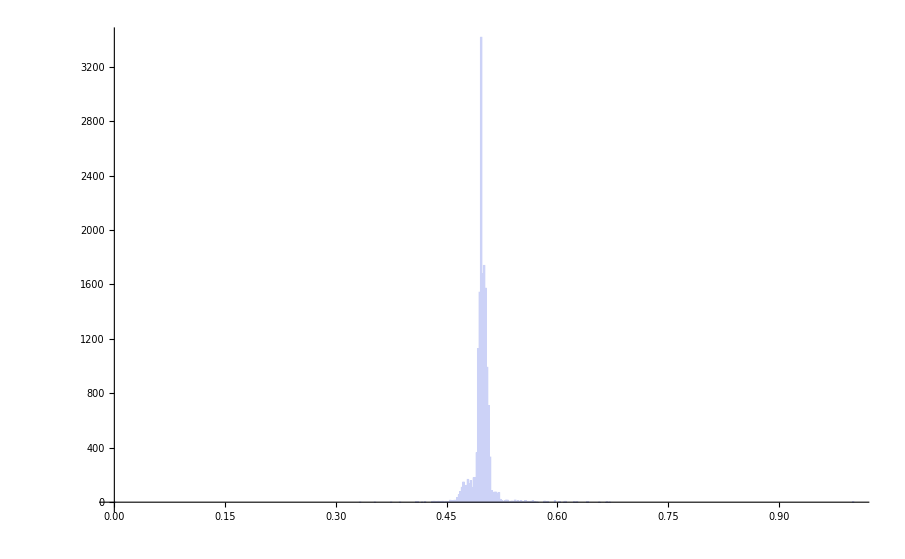
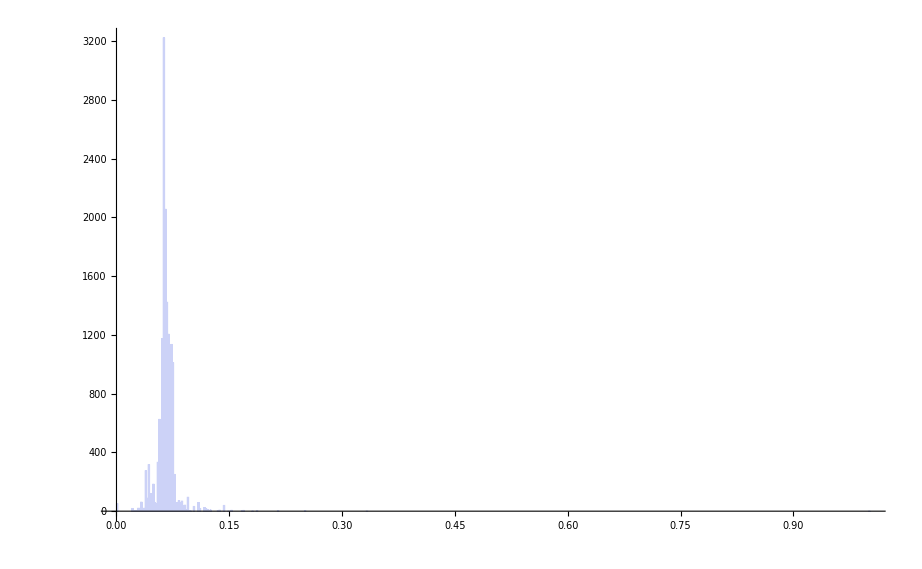
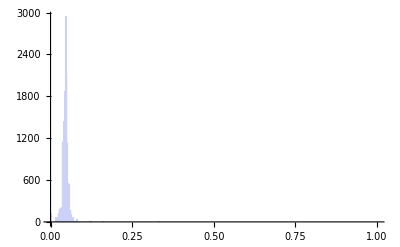
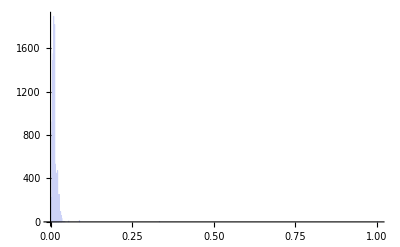
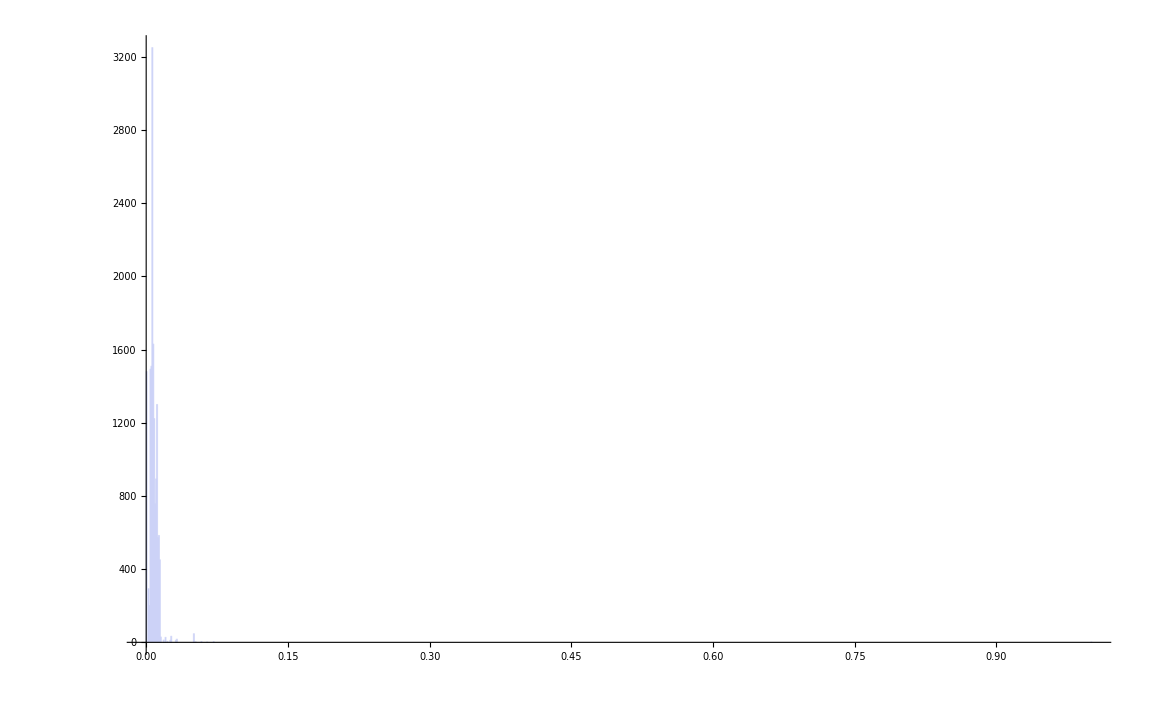

```mathematica
With[
{tuple={3,31,43,173,229}},
With[
{Vals=ReadList [FileNameForTupleBis[{3,31,43,173,229}]]},
Table[
Histogram[
Table[
DigitRatio[IntegerDigits[v,p],1],{v,Vals}
]
],
{p,tuple}
]
]
]
```

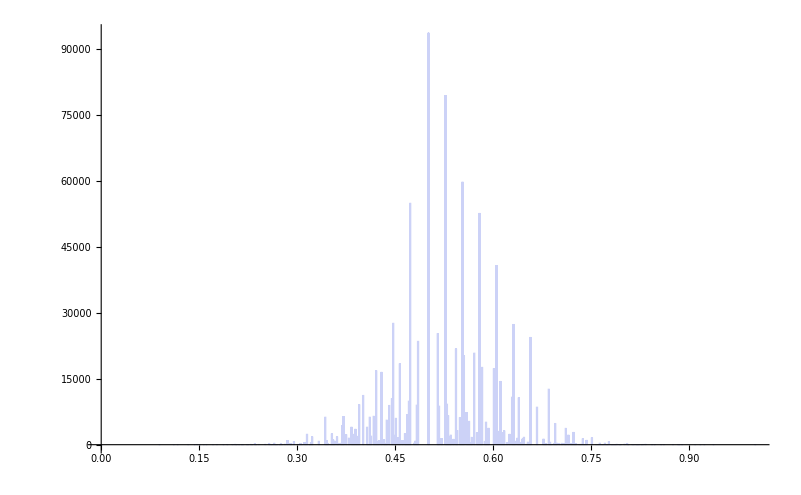
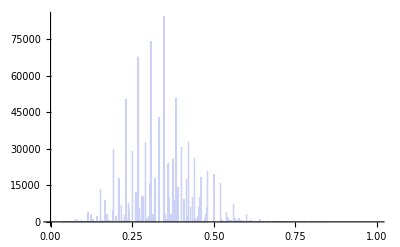

```mathematica
With[
{tuple={3,5}},
With[
{Vals=ReadList [FileNameForTuple[tuple],Number,1000000]},
Table[
Histogram[
Table[
DigitRatio[IntegerDigits[v,p],1],{v,Vals}
]
],
{p,tuple}
]
]
]
```